# Graph coloring package

## Loading the package

Remember:

The file graphcoloring.wl must be in the same folder that your notebook file.

You must change the directory where Mathematica searchs packages (to the current one).

Typically, save first the notebook and then load the package as follows:

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<graphcoloring.wl
```

## Examples

First, let’s create a graph using mathematica built-in function Graph[]

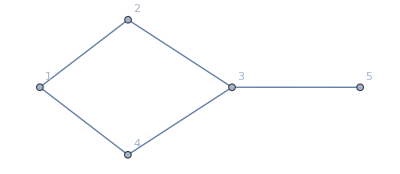

```mathematica
G1=Graph[{1<->2,2<->3,3<->4,4<->1,3<->5},VertexLabels->"Index"]
```

Now, let’s use the package. It has only one function, colorGraph[]. Its arguments are:

The graph you want to color.

The number of colors you want to use. You can only choose 3 or 4 as the number of colors.

```mathematica
colorGraph[G1,3]
```

Another example:

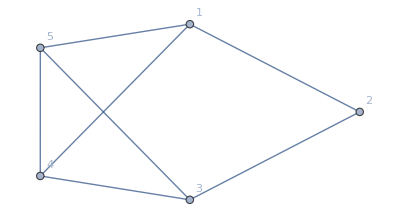

```mathematica
G2=Graph[{1<->2,2<->3,3<->4,4<->1,1<->5,3<->5,4<->5},VertexLabels->"Index"]
```

```mathematica
colorGraph[G2,4]
```